Curtis Sera
v 2.0
2019 - 10 - 11

# Bending energy of a toroidal pore

Solving the bending energy of a torus (ie the maximum energy conformation of a fusion pore)
Per MB Jackson (2010), a toroidal pore is a maximum energy conformation

Assume 0 spontaneous curvature for membrane
For complete work & derivations, see OneNote\Welch Lab\Work\Toroid Gbend 3

This notebook will compare 2 approaches, both in cylindrical coordinates:
A) Solving based on finding an expression for the distance between the z axis and the torus inner surface then spinning that around the z axis
	** z = 0 here set to the torus bottom
B) Solving based on a  parametrizing the surface integral so that it’s in terms of theta (renamed alpha) and the angle beta as below
	** z = 0 here set to the torus transverse midplane
-Graphics- 

Mathematica reminders/notes:
- () are for grouping, [] are for functions
- Functions conventionally start with CAPS.  Ie write Cos[], not cos[]

Definitions:
	r ~ distance b/w torus central axis & torus surface at that height
	R0 ~ torus ring radius
	t ~ tube radius (how thick the donut is)
	b ~ angle from midplane where 0 is the outer intersection b/w torus surface & midplane
	Kb ~ bending modulus

Graphing the surface:
First, let’s construct and graph the surface we’re computing things for so that we have something to project our results onto

20-5 √(1-1/25 (5-z)^2)

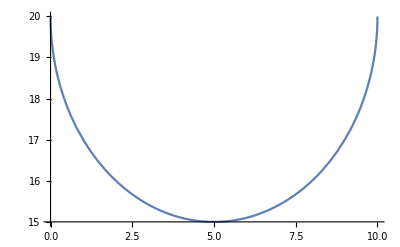

-Graphics3D-

```mathematica
t = 5;  (*Radius of the torus's tube = distance b/w membranes; nm*)
R0 = 20;  (*Radius of the circle a tube is bent into to make a torus; nm*)
Kb = 15;  (*Helfrich bending constant; k(_B)T*)

r[z_] := R0-t Cos[ArcSin[(t-z)/t]];(*torus's local radius of curvature in plane of R*)

torus = r[z]
Plot[torus,{z,0,2*t}]
RevolutionPlot3D[{torus,z},{z,0,2*t}] 
	(*Note how we put pwR as "x" and put z last to make it the axis of revolution*)
```

Method A: Bending energy by torus profile 
Great!
Now let’s compute the bending energy (which induces an equivalent tension)...

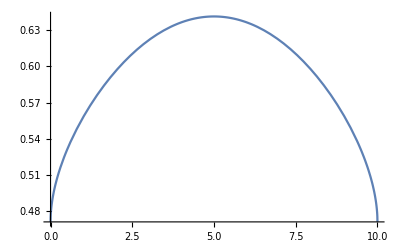

```mathematica
GbendA[z_]:= 2*Pi*Kb*0.5*(((1/R0)+(1/r[z]))^2) (*Expression has been integrated circularly over theta (ie around the z axis) -> 2*Pi *)

Plot[GbendA[z],{z,0,2*t}]
```

Next, we' ll re - graph our surface using above tension function as the coloring guide
- Color with normalized values

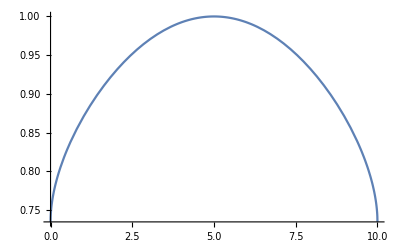

-Graphics3D-

```mathematica
GbendNormA[z_]:=GbendA[z]/GbendA[t] (*Normalize Gbend for graph coloring purposes*)
Plot[GbendNormA[z],{z,0,2*t}]

tension3dPlot=RevolutionPlot3D[{torus,z},{z,0,2*t},
ColorFunction->Function[{x,y,z},
Hue[2(1-GbendNormA[z])/3]],ColorFunctionScaling->False]
```

Notes on Hue[]: 
- To make red correspond to the highest tension, we’ve inverted the scale via 1-GbendNormA[z]
- To fix the default scheme’s color weirdness (they have magenta/violet as the min which looks a lot like the max’s red), we’ve done 2/3 to basically cut out the magenta

Finally, let' s use the above expression to get the torus' s total energy

```mathematica
Sum[GbendA[z],{z,0,2*t}]
```

6.4093

Method B: surface integral in parametric space

Note on integration in Mathematica:
- Integrate[f,x1,x2] can do definite or indefinite integration (see docs). Note that the integration order works left to right.
	- Eg Integrate[f,{x,0,Pi},{y,Pi/2,Pi}] --> does SS f() dx dy

1/150 π (15+450 π+272 √15 ArcTan[√(5/3)])

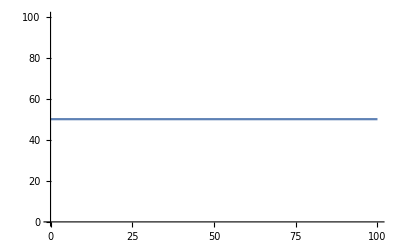

```mathematica
GbendB1= Integrate[Kb*t*(1/t+1/(R0-t*Cos[b]))^2,{a,0,2*Pi},{b,0,Pi/2}]
Plot[GbendB1,{t0,0,100}]
```

The above should be equivalent to integrating over alpha then over beta which is functionally equivalent to the order used in method A.
Let’s check this

```mathematica
GbendB1check= Integrate[2*Pi*Kb*t*(1/t+1/(R0-t*Cos[b]))^2,{b,0,Pi/2}]
Plot[GbendB1check,{t0,0,100}]
```

1/150 π (15+450 π+272 √15 ArcTan[√(5/3)])

-Graphics-

Great! Mathematica is integrating in the order I intended.
The surface integral should have interchangeable order of integration. Let’s check that

```mathematica
GbendB2=Integrate[Kb*t*(1/t+1/(R0-t*Cos[b]))^2,{b,0,Pi/2},{a,0,2*Pi}]
Plot[GbendB2,{t0,0,100}]
```

1/150 π (15+450 π+272 √15 ArcTan[√(5/3)])

-Graphics-